# Parental effects when selection is frequency-dependent

Bram Kuijper & Rufus A. Johnstone

```mathematica
Clear["Global`*"]
```

## Patch frequencies

f_i is the frequency of patches with i ∈ {0,1,2} hawks and hence 2-i doves.

b_(h,i) is the probability that a juvenile hawk is winning the vacant breeding spot in a patch that originally consisted of i hawks and hence 2-i doves, before mortality of one of the breeders.

```mathematica
bh[i_]:=((1-d)(i phh[i]+(2-i)pdh[i])+d Sum[f[k] (k phh[k]+(2-k)pdh[k]),{k,0,2}])/2;
```

change in patches containing 0 hawks:

```mathematica
df0dt=mh[1] f[1](1-bh[1])-2 md[0]f[0]bh[0];
```

change in patches containing 1 hawk:

```mathematica
df1dt=2md[0]f[0]bh[0]+2mh[2]f[2](1-bh[2])-mh[1]f[1](1-bh[1])-md[1]f[1]bh[1];
```

change in patches containing 2 hawks:

```mathematica
df2dt=md[1]f[1]bh[1]-2mh[2]f[2](1-bh[2]);
```

```mathematica
dfconstraint=f[0]+f[1]+f[2]==1;
```

```mathematica
ans[{ds_},{mh1_,mh2_},{md0_,md1_},{phhs_,pdhs_}]:=
FindRoot[{dfconstraint,df1dt==0,df2dt==0}/.{d->ds,mh[1]->mh1,mh[2]->mh2,md[0]->md0,md[1]->md1,md[2]->md2,phh[0]->phhs,phh[1]->phhs,phh[2]->phhs,pdh[0]->pdhs,pdh[1]->pdhs,pdh[2]->pdhs},{f[0],1/3},{f[1],1/3},{f[2],1/3}]
```

```mathematica
ansalt[{ds_},{mh1_,mh2_},{md0_,md1_},{phhs_,pdhs_}]:=
FindRoot[{df0dt==0,df1dt==0,dfconstraint}/.{d->ds,mh[1]->mh1,mh[2]->mh2,md[0]->md0,md[1]->md1,md[2]->md2,phh[0]->phhs,phh[1]->phhs,phh[2]->phhs,pdh[0]->pdhs,pdh[1]->pdhs,pdh[2]->pdhs},{f[0],1/3},{f[1],1/3},{f[2],1/3}]
```

```mathematica
vx=0.25;
cx=0.8;
```

```mathematica
ans[{0.1},{1.0-vx,1.0-.5*(vx-cx)},{1.0,1.0-.5*vx},{0.35,1.0}]
```

{f[0]→0.0859182,f[1]→0.667665,f[2]→0.246417}

```mathematica
ansalt[{0.1},{0.75,1.275},{0.875,1},{0.5,0.5}]
```

{f[0]→0.235385,f[1]→0.549231,f[2]→0.215385}

## Reproductive values

### Dynamics of v_(h,1), the reproductive value of a focal hawk in a patch with a dove

Mortality of focal hawk and replaced by focal’s offspring of type dove (producing a hawk would result in no change in RV)

```mathematica
dvh1dt1=mh[1] 1/2(1-d)(1-phh[1])(vd[0]-vh[1]);
```

Mortality of focal hawk and replaced by nonfocal offspring

```mathematica
dvh1dt2=mh[1](1/2(1-d)+d)(-vh[1]);
```

Mortality of the nonfocal dove and replaced by focal’s offspring of type dove

```mathematica
dvh1dt3=md[1] 1/2(1-d)(1-phh[1])vd[1];
```

Mortality of the nonfocal dove and replaced by focal’s offspring of type hawk

```mathematica
dvh1dt4=md[1] 1/2(1-d)phh[1](2vh[2]-vh[1]);
```

Mortality of the nonfocal dove and replaced by nonfocal offspring of type hawk

```mathematica
dvh1dt5=md[1](1/2(1-d)pdh[1]+1/2 d Sum[f[k](k phh[k]+(2-k)pdh[k]),{k,0,2}])(vh[2]-vh[1]);
```

Mortality of a remote hawk, replaced by focal’s offspring

```mathematica
dvh1dt6=Sum[f[k]k mh[k] 1/2 d (phh[1]vh[k-1+1]+(1-phh[1])vd[k-1]),{k,1,2}];
```

Mortality of a remote dove, replaced by focal’s offspring

```mathematica
dvh1dt7=Sum[f[k](2-k) md[k] 1/2 d (phh[1]vh[k+1]+(1-phh[1])vd[k]),{k,0,1}];
```

```mathematica
dvh1dt=dvh1dt1+dvh1dt2+dvh1dt3+dvh1dt4+dvh1dt5+dvh1dt6+dvh1dt7;
```

```mathematica
dvh1dt/.{phh[1]->p,phh[2]->p,pdh[0]->p,pdh[1]->p,vh[1]->v,vh[2]->v,vd[0]->v,vd[1]->v,md[1]->m,mh[1]->m,mh[2]->m,md[0]->m}//Simplify
```

d m v (-1+f[0]+f[1]+f[2])

```mathematica
dvd1dt/.{phh[1]->p,phh[2]->p,pdh[0]->p,pdh[1]->p,vh[1]->v,vh[2]->v,vd[0]->v,vd[1]->v,md[1]->m,mh[1]->m,mh[2]->m,md[0]->m}//Simplify
```

dvd1dt

### Dynamics of v_(d,1), the reproductive value of a focal dove in a patch with a hawk

Mortality of focal dove and replaced by focal’s offspring of type hawk

```mathematica
dvd1dt1=md[1] 1/2(1-d)pdh[1](vh[2]-vd[1]);
```

Mortality of focal dove and replaced by nonfocal offspring

```mathematica
dvd1dt2=md[1](1/2(1-d)+d)(-vd[1]);
```

Mortality of nonfocal hawk and replaced by focal’s offspring of type hawk

```mathematica
dvd1dt3=mh[1] 1/2(1-d)pdh[1]vh[1];
```

Mortality of nonfocal hawk and replaced by focal’s offspring of type dove

```mathematica
dvd1dt4=mh[1] 1/2(1-d)(1-pdh[1])(2vd[0]-vd[1]);
```

Mortality of the nonfocal hawk and replacement by nonfocal offspring of type dove

```mathematica
dvd1dt5=mh[1] 1/2((1-d)(1-phh[1])+d Sum[f[k](k (1-phh[k])+(2-k)(1-pdh[k])),{k,0,2}])(vd[0]-vd[1]);
```

Mortality of a remote hawk, replaced by focal’s offspring

```mathematica
dvd1dt6=Sum[f[k]k mh[k] 1/2 d (pdh[1]vh[k-1+1]+(1-pdh[1])vd[k-1]),{k,1,2}];
```

Mortality of a remote dove, replaced by focal’s offspring

```mathematica
dvd1dt7=Sum[f[k](2-k) md[k] 1/2 d (pdh[1]vh[k+1]+(1-pdh[1])vd[k]),{k,0,1}];
```

```mathematica
dvd1dt=dvd1dt1+dvd1dt2+dvd1dt3+dvd1dt4+dvd1dt5+dvd1dt6+dvd1dt7;
```

### Dynamics of v_(d,0), the reproductive value of a focal dove in a patch with another dove

Mortality of focal dove, replaced by focal’s offspring of type hawk

```mathematica
dvd0dt1=md[0] 1/2(1-d)pdh[0](vh[1]-vd[0]);
```

Mortality of focal dove, replaced by nonfocal offspring

```mathematica
dvd0dt2=md[0](1/2(1-d)+d)(-vd[0]);
```

Mortality of nonfocal dove, replaced by focal’s offspring of type dove;

```mathematica
dvd0dt3=md[0] 1/2(1-d)(1-pdh[0])vd[0];
```

Mortality of nonfocal dove, replaced by focal’s offspring of type hawk;

```mathematica
dvd0dt4=md[0] 1/2(1-d)pdh[0](vh[1]+vd[1]-vd[0]);
```

Mortality of nonfocal dove, replaced by nonfocal offspring of type hawk;

```mathematica
dvd0dt5=md[0] 1/2((1-d)pdh[0]+d Sum[f[k](k phh[k]+(2-k)pdh[k]),{k,0,2}])(vd[1]-vd[0]);
```

Mortality of a remote hawk, replaced by focal’s offspring

```mathematica
dvd0dt6=Sum[f[k]k mh[k] 1/2 d (pdh[0]vh[k-1+1]+(1-pdh[0])vd[k-1]),{k,1,2}];
```

Mortality of a remote dove, replaced by focal’s offspring

```mathematica
dvd0dt7=Sum[f[k](2-k) md[k] 1/2 d (pdh[0]vh[k+1]+(1-pdh[0])vd[k]),{k,0,1}];
```

```mathematica
dvd0dt=dvd0dt1+dvd0dt2+dvd0dt3+dvd0dt4+dvd0dt5+dvd0dt6+dvd0dt7;
```

### Dynamics of v_(h,2), the reproductive value of a focal hawk in a patch with another hawk

Mortality of focal hawk, replaced by focal’s offspring of type dove

```mathematica
dvh2dt1=mh[2] 1/2(1-d)(1-phh[2])(vd[1]-vh[2]);
```

Mortality of focal hawk, replaced by nonfocal offspring

```mathematica
dvh2dt2=mh[2](1/2(1-d)+d)(-vh[2]);
```

Mortality of nonfocal hawk, replaced by focal’s offspring of type hawk;

```mathematica
dvh2dt3=mh[2] 1/2(1-d)phh[2]vh[2];
```

Mortality of nonfocal hawk, replaced by focal’s offspring of type dove;

```mathematica
dvh2dt4=mh[2] 1/2(1-d)(1-phh[2])(vh[1]+vd[1]-vh[2]);
```

Mortality of nonfocal hawk, replaced by nonfocal offspring of type dove;

```mathematica
dvh2dt5=mh[2] 1/2((1-d)(1-phh[2])+d Sum[f[k](k(1-phh[k])+(2-k)(1-pdh[k])),{k,0,2}])(vh[1]-vh[2]);
```

Mortality of a remote hawk, replaced by focal’s offspring

```mathematica
dvh2dt6=Sum[f[k]k mh[k] 1/2 d (phh[2]vh[k-1+1]+(1-phh[2])vd[k-1]),{k,1,2}];
```

Mortality of a remote dove, replaced by focal’s offspring

```mathematica
dvh2dt7=Sum[f[k](2-k) md[k] 1/2 d (phh[2]vh[k+1]+(1-phh[2])vd[k]),{k,0,1}];
```

```mathematica
dvh2dt=dvh2dt1+dvh2dt2+dvh2dt3+dvh2dt4+dvh2dt5+dvh2dt6+dvh2dt7;
```

### Numerical solutions

```mathematica
sysRV={dvh1dt==0,dvd1dt==0,dvd0dt==0,dvh2dt==0};
rvconstraint=1/2 f[1](vh[1]+vd[1])+f[0]vd[0]+f[2]vh[2]==1;
sysRVc1=ReplacePart[sysRV,1->rvconstraint]//Simplify;
sysRVc2=ReplacePart[sysRV,3->rvconstraint]//Simplify;
rvstart={{vh[1],1.0},{vd[1],1.0},{vd[0],1.0},{vh[2],1.0}};
```

```mathematica
sysRVc2
```

{1/2 ((-1+d) md[1] (-1+phh[1]) vd[1]+(-1+d) mh[1] (-1+phh[1]) (vd[0]-vh[1])-(1+d) mh[1] vh[1]+2 d f[0] md[0] (vd[0]-phh[1] vd[0]+phh[1] vh[1])+d f[1] mh[1] (vd[0]-phh[1] vd[0]+phh[1] vh[1])+(-1+d) md[1] phh[1] (vh[1]-2 vh[2])-md[1] (pdh[1]+d (2 f[0] pdh[0]+(-1+f[1]) pdh[1]+f[1] phh[1]+2 f[2] phh[2])) (vh[1]-vh[2])+d f[1] md[1] (vd[1]-phh[1] vd[1]+phh[1] vh[2])+2 d f[2] mh[2] (vd[1]-phh[1] vd[1]+phh[1] vh[2]))==0,mh[1] ((-3+2 pdh[1]+phh[1]) vd[0]-(-2+pdh[1]+phh[1]) vd[1]-pdh[1] vh[1])+md[1] ((1+pdh[1]) vd[1]-pdh[1] vh[2])+d (mh[1] ((3-2 pdh[1]-phh[1]+f[1] (-3+2 pdh[1]+phh[1])+2 f[2] (-1+phh[2])) vd[0]+(-2+pdh[1]+phh[1]-f[1] (-2+pdh[1]+phh[1])-2 f[2] (-1+phh[2])) vd[1]-(-1+f[1]) pdh[1] vh[1])+2 f[0] (mh[1] (-1+pdh[0]) (vd[0]-vd[1])+md[0] ((-1+pdh[1]) vd[0]-pdh[1] vh[1]))+((-1+f[1]) md[1]+2 f[2] mh[2]) ((-1+pdh[1]) vd[1]-pdh[1] vh[2]))==0,2 f[0] vd[0]+f[1] (vd[1]+vh[1])+2 f[2] vh[2]==2,2 mh[2] (-1+phh[2]) (vd[1]+vh[1]-2 vh[2])+d (2 f[0] (md[0] ((-1+phh[2]) vd[0]-phh[2] vh[1])+mh[2] (-1+pdh[0]) (vh[1]-vh[2]))+2 (-1+f[2]) mh[2] ((-1+phh[2]) vd[1]+(-1+phh[2]) vh[1]+vh[2]-2 phh[2] vh[2])+f[1] (mh[1] ((-1+phh[2]) vd[0]-phh[2] vh[1])+mh[2] (-2+pdh[1]+phh[1]) (vh[1]-vh[2])+md[1] ((-1+phh[2]) vd[1]-phh[2] vh[2])))==0}

```mathematica
solrv1=Solve[{2 f[0] vd[0]+f[1] (vd[1]+vh[1])+2 f[2] vh[2]==2,mh[1] ((-3+2 pdh[1]+phh[1]) vd[0]-(-2+pdh[1]+phh[1]) vd[1]-pdh[1] vh[1])+md[1] ((1+pdh[1]) vd[1]-pdh[1] vh[2])+d (mh[1] ((3-2 pdh[1]-phh[1]+f[1] (-3+2 pdh[1]+phh[1])+2 f[2] (-1+phh[2])) vd[0]+(-2+pdh[1]+phh[1]-f[1] (-2+pdh[1]+phh[1])-2 f[2] (-1+phh[2])) vd[1]-(-1+f[1]) pdh[1] vh[1])+2 f[0] (mh[1] (-1+pdh[0]) (vd[0]-vd[1])+md[0] ((-1+pdh[1]) vd[0]-pdh[1] vh[1]))+((-1+f[1]) md[1]+2 f[2] mh[2]) ((-1+pdh[1]) vd[1]-pdh[1] vh[2]))==0,1/2 (2 md[0] pdh[0] (-2 vd[0]+vd[1]+vh[1])+d (md[0] (-(2-4 pdh[0]+f[0] (-2+4 pdh[0])+f[1] pdh[1]+f[1] phh[1]+2 f[2] phh[2]) vd[0]+(f[1] (pdh[1]+phh[1])+2 f[2] phh[2]) vd[1]+2 (-1+f[0]) pdh[0] (vd[1]+vh[1]))+2 f[2] mh[2] (vd[1]-pdh[0] vd[1]+pdh[0] vh[2])+f[1] (mh[1] (vd[0]-pdh[0] vd[0]+pdh[0] vh[1])+md[1] (vd[1]-pdh[0] vd[1]+pdh[0] vh[2]))))==0,2 mh[2] (-1+phh[2]) (vd[1]+vh[1]-2 vh[2])+d (2 f[0] (md[0] ((-1+phh[2]) vd[0]-phh[2] vh[1])+mh[2] (-1+pdh[0]) (vh[1]-vh[2]))+2 (-1+f[2]) mh[2] ((-1+phh[2]) vd[1]+(-1+phh[2]) vh[1]+vh[2]-2 phh[2] vh[2])+f[1] (mh[1] ((-1+phh[2]) vd[0]-phh[2] vh[1])+mh[2] (-2+pdh[1]+phh[1]) (vh[1]-vh[2])+md[1] ((-1+phh[2]) vd[1]-phh[2] vh[2])))==0},{vh[1],vd[1],vd[0],vh[2]}]//Flatten;
```

```mathematica
solrv2=Solve[{1/2 ((-1+d) md[1] (-1+phh[1]) vd[1]+(-1+d) mh[1] (-1+phh[1]) (vd[0]-vh[1])-(1+d) mh[1] vh[1]+2 d f[0] md[0] (vd[0]-phh[1] vd[0]+phh[1] vh[1])+d f[1] mh[1] (vd[0]-phh[1] vd[0]+phh[1] vh[1])+(-1+d) md[1] phh[1] (vh[1]-2 vh[2])-md[1] (pdh[1]+d (2 f[0] pdh[0]+(-1+f[1]) pdh[1]+f[1] phh[1]+2 f[2] phh[2])) (vh[1]-vh[2])+d f[1] md[1] (vd[1]-phh[1] vd[1]+phh[1] vh[2])+2 d f[2] mh[2] (vd[1]-phh[1] vd[1]+phh[1] vh[2]))==0,mh[1] ((-3+2 pdh[1]+phh[1]) vd[0]-(-2+pdh[1]+phh[1]) vd[1]-pdh[1] vh[1])+md[1] ((1+pdh[1]) vd[1]-pdh[1] vh[2])+d (mh[1] ((3-2 pdh[1]-phh[1]+f[1] (-3+2 pdh[1]+phh[1])+2 f[2] (-1+phh[2])) vd[0]+(-2+pdh[1]+phh[1]-f[1] (-2+pdh[1]+phh[1])-2 f[2] (-1+phh[2])) vd[1]-(-1+f[1]) pdh[1] vh[1])+2 f[0] (mh[1] (-1+pdh[0]) (vd[0]-vd[1])+md[0] ((-1+pdh[1]) vd[0]-pdh[1] vh[1]))+((-1+f[1]) md[1]+2 f[2] mh[2]) ((-1+pdh[1]) vd[1]-pdh[1] vh[2]))==0,2 f[0] vd[0]+f[1] (vd[1]+vh[1])+2 f[2] vh[2]==2,2 mh[2] (-1+phh[2]) (vd[1]+vh[1]-2 vh[2])+d (2 f[0] (md[0] ((-1+phh[2]) vd[0]-phh[2] vh[1])+mh[2] (-1+pdh[0]) (vh[1]-vh[2]))+2 (-1+f[2]) mh[2] ((-1+phh[2]) vd[1]+(-1+phh[2]) vh[1]+vh[2]-2 phh[2] vh[2])+f[1] (mh[1] ((-1+phh[2]) vd[0]-phh[2] vh[1])+mh[2] (-2+pdh[1]+phh[1]) (vh[1]-vh[2])+md[1] ((-1+phh[2]) vd[1]-phh[2] vh[2])))==0},{vh[1],vd[1],vd[0],vh[2]}]//Flatten;
```

```mathematica
ansRV[{ds_},{mh1_,mh2_},{md0_,md1_},{phhs_,pdhs_}]:=Module[{freqs},
freqs=ans[{ds},{mh1,mh2},{md0,md1},{phhs,pdhs}];
solrv1/.freqs/.{d->ds,mh[1]->mh1,mh[2]->mh2,md[0]->md0,md[1]->md1,md[2]->md2,phh[0]->phhs,phh[1]->phhs,phh[2]->phhs,pdh[0]->pdhs,pdh[1]->pdhs,pdh[2]->pdhs}
]
```

```mathematica
ansRValt[{ds_},{mh1_,mh2_},{md0_,md1_},{phhs_,pdhs_}]:=Module[{freqs},
freqs=ans[{ds},{mh1,mh2},{md0,md1},{phhs,pdhs}];
solrv2/.freqs/.{d->ds,mh[1]->mh1,mh[2]->mh2,md[0]->md0,md[1]->md1,md[2]->md2,phh[0]->phhs,phh[1]->phhs,phh[2]->phhs,pdh[0]->pdhs,pdh[1]->pdhs,pdh[2]->pdhs}
]
```

```mathematica
ansRVtest[{ds_},{mh1_,mh2_},{md0_,md1_},{phhs_,pdhs_}]:=Module[{freqs},
freqs=ans[{ds},{mh1,mh2},{md0,md1},{phhs,pdhs}]; 
Return[sysRVc1/.freqs/.{d->ds,mh[1]->mh1,mh[2]->mh2,md[0]->md0,md[1]->md1,md[2]->md2,phh[0]->phhs,phh[1]->phhs,phh[2]->phhs,pdh[0]->pdhs,pdh[1]->pdhs,pdh[2]->pdhs}/.{vh[1]->1.0,vd[1]->1.0,vd[0]->1.0,vh[2]->1.0}];
]
```

```mathematica
ansRVtest[{0.1},{1.0,3.0},{2.0,1.0},{0.1,0.5}]
```

{True,False,False,False}

```mathematica
out=ansRValt[{0.5},{1.0,2.0},{2.0,1.0},{0.25,0.9}]
```

{vh[1]→1.03386,vd[1]→1.04126,vd[0]→0.912001,vh[2]→0.896732}

```mathematica
out=ansRV[{0.5},{1.0,2.0},{2.0,1.0},{0.25,0.9}]
```

{vh[1]→1.03386,vd[1]→1.04126,vd[0]→0.912001,vh[2]→0.896732}

## Relatedness coefficients

### Relatedness between two hawks

Hawk dies on a site with two hawks, replaced by a new hawk

```mathematica
drhhdt1=2mh[2]f[2](1/2(1-d)phh[2](1/2+1/2 rhh));
```

Dove dies on a site with one hawk, one dove, replaced by hawk

```mathematica
drhhdt2=md[1]f[1](1/2(1-d)pdh[1]rhd+1/2(1-d)phh[1]);
```

```mathematica
drhhdt=rhh==drhhdt1+drhhdt2;
```

### Relatedness between hawk and dove

Hawk dies on a site with two hawks, replaced by dove

```mathematica
drhddt1=2mh[2]f[2](1/2(1-d)(1-phh[2])(1/2+1/2 rhh));
```

Dove dies on a site with a hawk and dove, replaced by dove

```mathematica
drhddt2=md[1]f[1](1/2(1-d)(1-pdh[1])rhd+1/2(1-d)(1-phh[1]));
```

Hawk dies on a site with a hawk and dove, replaced by hawk

```mathematica
drhddt3=mh[1]f[1](1/2(1-d)pdh[1]+1/2(1-d)phh[1]rhd);
```

Dove dies on a site with two doves, replaced by hawk

```mathematica
drhddt4=2md[0]f[0](1/2(1-d)pdh[0](1/2+1/2 rdd));
```

```mathematica
drhddt=rhd==drhddt1+drhddt2+drhddt3+drhddt4;
```

### Relatedness between two doves

Dove dies on a site with two doves, replaced by dove

```mathematica
drdddt1=2 md[0]f[0](1/2(1-d)(1-pdh[0])(1/2+1/2 rdd));
```

Hawk dies on a site with a hawk and a dove

```mathematica
drdddt2=mh[1]f[1](1/2(1-d)(1-phh[1])rhd+1/2(1-d)(1-pdh[1]));
```

```mathematica
drdddt=rdd==drdddt1+drdddt2;
```

### Solving the relatedness equations

```mathematica
drdddt1+drdddt2//Variables
```

{d,rdd,f[0],md[0],pdh[0],f[1],mh[1],pdh[1],rhd,phh[1]}

```mathematica
rsols=Solve[{drhhdt,drhddt,drdddt},{rdd,rhd,rhh}]//Flatten;
```

```mathematica
rdd/.rsols//Variables
rhd/.rsols//Variables
rhh/.rsols//Variables
```

{d,f[0],f[1],md[0],mh[1],pdh[0],phh[1],f[2],mh[2],phh[2],md[1],pdh[1]}

{f[1],mh[1],f[0],md[0],pdh[0],pdh[1],phh[1],d,f[2],mh[2],phh[2],md[1]}

{d,md[1],mh[1],pdh[1],f[0],md[0],f[1],pdh[0],phh[1],f[2],mh[2],phh[2]}

```mathematica
rdd-rhh/.rsols/.{md[0]->m,md[1]->m,mh[1]->m,mh[2]->m,phh[1]->p,phh[2]->p,pdh[0]->p,pdh[1]->p,f[0]->x,f[1]->x,f[2]->x}//Simplify
```

(4 (-1+d) m (-1+2 p) x)/(4+4 (-1+d) m x+(-1+d)^2 m^2 (1-p+p^2) x^2)

```mathematica
rhh/.rsols/.{md[0]->m,md[1]->m,mh[1]->m,mh[2]->m,phh[1]->p,phh[2]->p,pdh[0]->p,pdh[1]->p,f[0]->x,f[1]->x,f[2]->x}//Simplify
```

(2 (-1+d) m p x (-2+(-1+d) m (-1+p) x))/(4+4 (-1+d) m x+(-1+d)^2 m^2 (1-p+p^2) x^2)

```mathematica
rhh/.rsols
```

-((1-d) md[1] pdh[1] (-f[0] md[0]-f[1] mh[1]+f[0] md[0] pdh[0]+f[1] mh[1] pdh[1]))/(2 mh[1] (-1+phh[1]) (1-1/2 (1-d) f[2] mh[2] phh[2]))-(-f[1] md[1] phh[1]+d f[1] md[1] phh[1]-f[2] mh[2] phh[2]+d f[2] mh[2] phh[2])/(2-f[2] mh[2] phh[2]+d f[2] mh[2] phh[2])-(md[1] (1-1/2 (1-d) f[0] md[0] (1-pdh[0])) pdh[1] (-(-1/2 (1-d) f[0] md[0] (1-pdh[0])-1/2 (1-d) f[1] mh[1] (1-pdh[1])) (-1/4 (1-d)^2 f[1] f[2] md[1] mh[2] pdh[1] (1-phh[2])+(1-1/2 (1-d) f[1] md[1] (1-pdh[1])-1/2 (1-d) f[1] mh[1] phh[1]) (1-1/2 (1-d) f[2] mh[2] phh[2]))-1/2 (1-d) f[1] mh[1] (1-phh[1]) ((-1/2 (1-d) f[0] md[0] pdh[0]-1/2 (1-d) f[1] mh[1] pdh[1]-1/2 (1-d) f[1] md[1] (1-phh[1])-1/2 (1-d) f[2] mh[2] (1-phh[2])) (1-1/2 (1-d) f[2] mh[2] phh[2])+1/2 (1-d) f[2] mh[2] (1-phh[2]) (-1/2 (1-d) f[1] md[1] phh[1]-1/2 (1-d) f[2] mh[2] phh[2]))))/(mh[1] (1-phh[1]) (1-1/2 (1-d) f[2] mh[2] phh[2]) (1/4 (1-d)^2 f[0] f[1] md[0] mh[1] pdh[0] (1-phh[1]) (1-1/2 (1-d) f[2] mh[2] phh[2])-(1-1/2 (1-d) f[0] md[0] (1-pdh[0])) (-1/4 (1-d)^2 f[1] f[2] md[1] mh[2] pdh[1] (1-phh[2])+(1-1/2 (1-d) f[1] md[1] (1-pdh[1])-1/2 (1-d) f[1] mh[1] phh[1]) (1-1/2 (1-d) f[2] mh[2] phh[2]))))

Some numerical exmples

```mathematica
ansRel[{ds_},{mh1_,mh2_},{md0_,md1_},{phhs_,pdhs_}]:=Module[{freqs},
freqs=ans[{ds},{mh1,mh2},{md0,md1},{phhs,pdhs}]; 
Return[rsols/.freqs/.{d->ds,mh[1]->mh1,mh[2]->mh2,md[0]->md0,md[1]->md1,md[2]->md2,phh[0]->phhs,phh[1]->phhs,phh[2]->phhs,pdh[0]->pdhs,pdh[1]->pdhs,pdh[2]->pdhs}];
];
```

```mathematica
ansRel[{0.01},{1.0-vx,1.0-.5*(vx-cx)},{1.0-.5*cx,1.0},{0.35,1.0}]
```

{rdd→0.100174,rhd→0.669549,rhh→0.390758}

## Selection gradient phh

### D[v_(h,1),phh], effect of mutant hawk on its reproductive value when in patch with a dove

Mortality of focal hawk and replaced by focal’s offspring of type dove (producing a hawk would result in no change in RV)

```mathematica
dvh1dt1δ=mh[1] 1/2(1-d)(1-(phh[1]+δphh[1]))(vd[0]-vh[1]);
```

Mortality of focal hawk and replaced by nonfocal offspring

```mathematica
dvh1dt2δ=mh[1](1/2(1-d)+d)(-vh[1]);
```

Mortality of the nonfocal dove and replaced by focal’s offspring of type dove

```mathematica
dvh1dt3δ=md[1] 1/2(1-d)(1-(phh[1]+δphh[1]))vd[1];
```

Mortality of the nonfocal dove and replaced by focal’s offspring of type hawk

```mathematica
dvh1dt4δ=md[1] 1/2(1-d)(phh[1]+δphh[1])(2vh[2]-vh[1]);
```

Mortality of the nonfocal dove and replaced by nonfocal offspring of type hawk

```mathematica
dvh1dt5δ=md[1](1/2(1-d)pdh[1]+1/2 d Sum[f[k](k phh[k]+(2-k)pdh[k]),{k,0,2}])(vh[2]-vh[1]);
```

Mortality of a remote hawk, replaced by focal’s offspring

```mathematica
dvh1dt6δ=Sum[f[k]k mh[k] 1/2 d ((phh[1]+δphh[1])vh[k-1+1]+(1-(phh[1]+δphh[1]))vd[k-1]),{k,1,2}];
```

Mortality of a remote dove, replaced by focal’s offspring

```mathematica
dvh1dt7δ=Sum[f[k](2-k) md[k] 1/2 d ((phh[1]+δphh[1])vh[k+1]+(1-(phh[1]+δphh[1]))vd[k]),{k,0,1}];
```

```mathematica
dvh1dtδ=dvh1dt1δ+dvh1dt2δ+dvh1dt3δ+dvh1dt4δ+dvh1dt5δ+dvh1dt6δ+dvh1dt7δ;
```

### D[v_(d,1),phh], effect of mutant dove on its reproductive value when in patch with a hawk

Mortality of focal dove and replaced by focal’s offspring of type hawk

```mathematica
dvd1dt1δ=md[1] 1/2(1-d)pdh[1](vh[2]-vd[1]);
```

Mortality of focal dove and replaced by nonfocal offspring

```mathematica
dvd1dt2δ=md[1](1/2(1-d)+d)(-vd[1]);
```

Mortality of nonfocal hawk and replaced by focal’s offspring of type hawk

```mathematica
dvd1dt3δ=mh[1] 1/2(1-d)pdh[1]vh[1];
```

Mortality of nonfocal hawk and replaced by focal’s offspring of type dove

```mathematica
dvd1dt4δ=mh[1] 1/2(1-d)(1-pdh[1])(2vd[0]-vd[1]);
```

Mortality of the nonfocal hawk and replacement by nonfocal offspring of type dove

```mathematica
dvd1dt5δ=mh[1] 1/2((1-d)(1-(phh[1]+rhd δphh[1]))+d Sum[f[k](k (1-phh[k])+(2-k)(1-pdh[k])),{k,0,2}])(vd[0]-vd[1]);
```

Mortality of a remote hawk, replaced by focal’s offspring

```mathematica
dvd1dt6δ=Sum[f[k]k mh[k] 1/2 d (pdh[1]vh[k-1+1]+(1-pdh[1])vd[k-1]),{k,1,2}];
```

Mortality of a remote dove, replaced by focal’s offspring

```mathematica
dvd1dt7δ=Sum[f[k](2-k) md[k] 1/2 d (pdh[1]vh[k+1]+(1-pdh[1])vd[k]),{k,0,1}];
```

```mathematica
dvd1dtδ=dvd1dt1δ+dvd1dt2δ+dvd1dt3δ+dvd1dt4δ+dvd1dt5δ+dvd1dt6δ+dvd1dt7δ;
```

### D[v_(h,2),phh] effect on reproductive value of a mutant focal hawk in a patch with another hawk

Mortality of focal hawk, replaced by focal’s offspring of type dove

```mathematica
dvh2dt1δ=mh[2] 1/2(1-d)(1-(phh[2]+δphh[2]))(vd[1]-vh[2]);
```

Mortality of focal hawk, replaced by nonfocal offspring

```mathematica
dvh2dt2δ=mh[2](1/2(1-d)+d)(-vh[2]);
```

Mortality of nonfocal hawk, replaced by focal’s offspring of type hawk;

```mathematica
dvh2dt3δ=mh[2] 1/2(1-d)(phh[2]+δphh[2])vh[2];
```

Mortality of nonfocal hawk, replaced by focal’s offspring of type dove;

```mathematica
dvh2dt4δ=mh[2] 1/2(1-d)(1-(phh[2]+δphh[2]))(vh[1]+vd[1]-vh[2]);
```

Mortality of nonfocal hawk, replaced by nonfocal offspring of type dove;

```mathematica
dvh2dt5δ=mh[2] 1/2((1-d)(1-(phh[2]+rhh δphh[2]))+d Sum[f[k](k(1-phh[k])+(2-k)(1-pdh[k])),{k,0,2}])(vh[1]-vh[2]);
```

Mortality of a remote hawk, replaced by focal’s offspring

```mathematica
dvh2dt6δ=Sum[f[k]k mh[k] 1/2 d ((phh[2]+δphh[2])vh[k-1+1]+(1-(phh[2]+δphh[2]))vd[k-1]),{k,1,2}];
```

Mortality of a remote dove, replaced by focal’s offspring

```mathematica
dvh2dt7δ=Sum[f[k](2-k) md[k] 1/2 d ((phh[2]+δphh[2])vh[k+1]+(1-(phh[2]+δphh[2]))vd[k]),{k,0,1}];
```

```mathematica
dvh2dtδ=dvh2dt1δ+dvh2dt2δ+dvh2dt3δ+dvh2dt4δ+dvh2dt5δ+dvh2dt6δ+dvh2dt7δ;
```

```mathematica
D[dvh2dtδ,δphh[2]]/.δphh[2]->0//Simplify
```

1/2 (-mh[2] (2 vd[1]+(1+rhh) vh[1]-(3+rhh) vh[2])+d (2 f[0] md[0] (-vd[0]+vh[1])+mh[2] (-2 (-1+f[2]) vd[1]+(1+rhh) vh[1]-(3+rhh-2 f[2]) vh[2])+f[1] (mh[1] (-vd[0]+vh[1])+md[1] (-vd[1]+vh[2]))))

### Final selection gradient on phh

```mathematica
gradphh=1/2 f[1](D[dvh1dtδ,δphh[1]]+D[dvd1dtδ,δphh[1]])+f[2](D[dvh2dtδ,δphh[2]]);
```

## Selection gradient pdh

### D[v_(h,1),pdh], effect of mutant hawk on its reproductive value when in patch with a dove

Mortality of focal hawk and replaced by focal’s offspring of type dove (producing a hawk would result in no change in RV)

```mathematica
dvh1dt1δpdh=mh[1] 1/2(1-d)(1-phh[1])(vd[0]-vh[1]);
```

Mortality of focal hawk and replaced by nonfocal offspring

```mathematica
dvh1dt2δpdh=mh[1](1/2(1-d)+d)(-vh[1]);
```

Mortality of the nonfocal dove and replaced by focal’s offspring of type dove

```mathematica
dvh1dt3δpdh=md[1] 1/2(1-d)(1-phh[1])vd[1];
```

Mortality of the nonfocal dove and replaced by focal’s offspring of type hawk

```mathematica
dvh1dt4δpdh=md[1] 1/2(1-d)phh[1](2vh[2]-vh[1]);
```

Mortality of the nonfocal dove and replaced by nonfocal offspring of type hawk

```mathematica
dvh1dt5δpdh=md[1](1/2(1-d)(pdh[1]+rhd δpdh[1])+1/2 d Sum[f[k](k phh[k]+(2-k)pdh[k]),{k,0,2}])(vh[2]-vh[1]);
```

Mortality of a remote hawk, replaced by focal’s offspring

```mathematica
dvh1dt6δpdh=Sum[f[k]k mh[k] 1/2 d (phh[1]vh[k-1+1]+(1-phh[1])vd[k-1]),{k,1,2}];
```

Mortality of a remote dove, replaced by focal’s offspring

```mathematica
dvh1dt7δpdh=Sum[f[k](2-k) md[k] 1/2 d (phh[1]vh[k+1]+(1-phh[1])vd[k]),{k,0,1}];
```

```mathematica
dvh1dtδpdh=dvh1dt1δpdh+dvh1dt2δpdh+dvh1dt3δpdh+dvh1dt4δpdh+dvh1dt5δpdh+dvh1dt6δpdh+dvh1dt7δpdh;
```

### D[v_(d,1),pdh], effect of mutant dove on its reproductive value when in patch with a hawk

Mortality of focal dove and replaced by focal’s offspring of type hawk

```mathematica
dvd1dt1δpdh=md[1] 1/2(1-d)(pdh[1]+δpdh[1])(vh[2]-vd[1]);
```

Mortality of focal dove and replaced by nonfocal offspring

```mathematica
dvd1dt2δpdh=md[1](1/2(1-d)+d)(-vd[1]);
```

Mortality of nonfocal hawk and replaced by focal’s offspring of type hawk

```mathematica
dvd1dt3δpdh=mh[1] 1/2(1-d)(pdh[1]+δpdh[1]) vh[1];
```

Mortality of nonfocal hawk and replaced by focal’s offspring of type dove

```mathematica
dvd1dt4δpdh=mh[1] 1/2(1-d)(1-(pdh[1]+δpdh[1]))(2vd[0]-vd[1]);
```

Mortality of the nonfocal hawk and replacement by nonfocal offspring of type dove

```mathematica
dvd1dt5δpdh=mh[1] 1/2((1-d)(1-phh[1])+d Sum[f[k](k (1-phh[k])+(2-k)(1-pdh[k])),{k,0,2}])(vd[0]-vd[1]);
```

Mortality of a remote hawk, replaced by focal’s offspring

```mathematica
dvd1dt6δpdh=Sum[f[k]k mh[k] 1/2 d ((pdh[1]+δpdh[1])vh[k-1+1]+(1-(pdh[1]+δpdh[1]))vd[k-1]),{k,1,2}];
```

Mortality of a remote dove, replaced by focal’s offspring

```mathematica
dvd1dt7δpdh=Sum[f[k](2-k) md[k] 1/2 d ((pdh[1]+δpdh[1])vh[k+1]+(1-(pdh[1]+δpdh[1]))vd[k]),{k,0,1}];
```

```mathematica
dvd1dtδpdh=dvd1dt1δpdh+dvd1dt2δpdh+dvd1dt3δpdh+dvd1dt4δpdh+dvd1dt5δpdh+dvd1dt6δpdh+dvd1dt7δpdh;
```

### D[v_(d,0),pdh], effect of mutant dove on its reproductive value when in patch with another dove

Mortality of focal dove, replaced by focal’s offspring of type hawk

```mathematica
dvd0dt1δpdh=md[0] 1/2(1-d)(pdh[0]+δpdh[0])(vh[1]-vd[0]);
```

Mortality of focal dove, replaced by nonfocal offspring

```mathematica
dvd0dt2δpdh=md[0](1/2(1-d)+d)(-vd[0]);
```

Mortality of nonfocal dove, replaced by focal’s offspring of type dove;

```mathematica
dvd0dt3δpdh=md[0] 1/2(1-d)(1-(pdh[0]+δpdh[0]))vd[0];
```

Mortality of nonfocal dove, replaced by focal’s offspring of type hawk;

```mathematica
dvd0dt4δpdh=md[0] 1/2(1-d)(pdh[0]+δpdh[0])(vh[1]+vd[1]-vd[0]);
```

Mortality of nonfocal dove, replaced by nonfocal offspring of type hawk;

```mathematica
dvd0dt5δpdh=md[0] 1/2((1-d)(pdh[0]+rdd δpdh[0])+d Sum[f[k](k phh[k]+(2-k)pdh[k]),{k,0,2}])(vd[1]-vd[0]);
```

Mortality of a remote hawk, replaced by focal’s offspring

```mathematica
dvd0dt6δpdh=Sum[f[k]k mh[k] 1/2 d ((pdh[0]+δpdh[0])vh[k-1+1]+(1-(pdh[0]+δpdh[0]))vd[k-1]),{k,1,2}];
```

Mortality of a remote dove, replaced by focal’s offspring

```mathematica
dvd0dt7δpdh=Sum[f[k](2-k) md[k] 1/2 d ((pdh[0]+δpdh[0])vh[k+1]+(1-(pdh[0]+δpdh[0]))vd[k]),{k,0,1}];
```

```mathematica
dvd0dtδpdh=dvd0dt1δpdh+dvd0dt2δpdh+dvd0dt3δpdh+dvd0dt4δpdh+dvd0dt5δpdh+dvd0dt6δpdh+dvd0dt7δpdh;
```

### Final selection gradient on pdh

```mathematica
gradpdh=1/2 f[1](D[dvh1dtδpdh,δpdh[1]]+D[dvd1dtδpdh,δpdh[1]])+f[0](D[dvd0dtδpdh,δpdh[0]]);
```

## Export to C for numerical iterations

```mathematica
toC[x_]:=ToString[CForm[x]];
```

```mathematica
destdir=$HomeDirectory<>"/Projects/parental_effects_freq_dep/src/numerical/simple/";
```

Recursions patch frequencies:

```mathematica
subslistp={phh[1]->phh,pdh[1]->pdh,pdh[0]->pdh,phh[2]->phh,f[2]->1-f[0]-f[1],md[0]->1-v/2,md[1]->1-0,mh[1]->1-v,mh[2]->1-(v/2-c/2)};
```

```mathematica
str="
double df0dt = 0;\n
double df1dt = 0;\n
for (int rtime=0;rtime<1e7;++rtime)
{\n
 df0dt="<>toC[f[0]+0.01*df0dt/.subslistp]<>";\n\n";
str=str<>"df1dt="<>toC[f[1]+0.01*df1dt/.subslistp]<>";\n\n";
str=str<>"if (fabs(df0dt-f(0))<1e-7 && fabs(df1dt-f(1))<1e-7)
{\n
f(0)=bound(df0dt);\n
f(1)=bound(df1dt);\n
break;
}
f(0)=bound(df0dt);\n
f(1)=bound(df1dt);\n
}\n";
str=str<>"gsl_vector_set(f,0,df0dt);\ngsl_vector_set(f,1,df1dt);";
Export[destdir<>"patchrecurs.txt",str];
```

Selection gradients:

```mathematica
str="double phhtplus1=bound("<>toC[phh+0.01*gradphh/.solrv2/.rsols/.subslistp]<>");\n\n";
str=str<>"double pdhtplus1=bound("<>toC[pdh+0.01*gradpdh/.solrv2/.rsols/.subslistp]<>");\n\n";
str=str<>"gsl_vector_set(f,0, phhtplus1);
\ngsl_vector_set(f,1, pdhtplus1);";
Export[destdir<>"selgrad.txt",str];
```

Parameters:

```mathematica
params={d,v,c};
variables=Join[params,{f[0],f[1],pdh,phh}];

str="";
For[iter=1,iter<=Length[params],iter++,
str=str<>"double "<>toC[params[[iter]]]<>";\n";
];
Export[destdir<>"params.txt",str];
str="";
For[iter=1,iter<=Length[variables],iter++,
str=str<>"double "<>toC[variables[[iter]]]<>";\n";
];
Export[destdir<>"variables.txt",str];
```

```mathematica
pdh+0.01*gradpdh/.solrv2/.rsols/.subslistp/.{f[0]->0.5,f[1]->0.5,v->0.25,c->0.5,phh->0.5,pdh->0.5,d->0.1}
```

0.500115

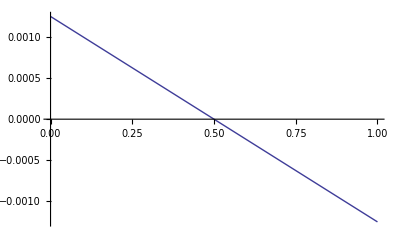

```mathematica
Plot[.01*df1dt/.solrv2/.rsols/.subslistp/.{f[1]->0.5,v->0.25,c->0.5,phh->0.5,pdh->0.5,d->0.1},{f[0],0,1.0}]
```

```mathematica
{md[0]->1-v/2,md[1]->1-0,mh[1]->1-v,mh[2]->1-(v/2-c/2)}/.{v->0.25,c->0.8}
```

{md[0]→0.875,md[1]→1,mh[1]→0.75,mh[2]→1.275}